# EOH Pos basis

#### Create the Hamiltonian in the position basis,

```mathematica
Xp:=N[SparseArray[{i_,i_}->√((2π)/8)(2i-9)/2,{8,8}]]
matpos:=Table[1/(√8)Exp[(2π)/8 ⅈ((2j-9)(2k-9))/4],{j,1,8},{k,1,8}]
Pp:=(ConjugateTranspose[matpos].Xp).matpos
HamiltonianPosEOHSHO :=  1/2 Pp.Pp+ 1/2  MatrixPower[Xp,2] 
Reverse[N[Eigenvalues[HamiltonianPosEOHSHO]]]
```

{0.500029,1.49925,2.5068,3.44784,4.69521,5.00797,6.53829,8.79133}

#### Chop it up because there were some very small (10^-17) values that Jupyter didn’t like,

```mathematica
HamiltonianPosEOHSHO=Chop[N[HamiltonianPosEOHSHO]]
```

{{6.87223,-1.2387,0.27768,-0.0880317,0,0.0880317,-0.27768,1.2387},{-1.2387,4.51604,-1.2387,0.27768,-0.0880317,0,0.0880317,-0.27768},{0.27768,-1.2387,2.94524,-1.2387,0.27768,-0.0880317,0,0.0880317},{-0.0880317,0.27768,-1.2387,2.15984,-1.2387,0.27768,-0.0880317,0},{0,-0.0880317,0.27768,-1.2387,2.15984,-1.2387,0.27768,-0.0880317},{0.0880317,0,-0.0880317,0.27768,-1.2387,2.94524,-1.2387,0.27768},{-0.27768,0.0880317,0,-0.0880317,0.27768,-1.2387,4.51604,-1.2387},{1.2387,-0.27768,0.0880317,0,-0.0880317,0.27768,-1.2387,6.87223}}

#### Save the Hamiltonian,

```mathematica
SetDirectory[NotebookDirectory[]];
saveHam[ham_]:=Export["./"<>"Hamposbh.txt",ham,"Table"]
saveHam[HamiltonianPosEOHSHO];
```

#### Classical computations of the EOH

```mathematica
MatrixExp[-ⅈ t  HamiltonianPosEOHSHO][[1,1]]
```

(-0.00448881-0.00308355 ⅈ) ((0.+0. ⅈ)-(0.00448881-0.00308355 ⅈ) (ⅇ^(-5.56194×10^-17 t) Cos[0.500029 t]-ⅈ ⅇ^(-5.56194×10^-17 t) Sin[0.500029 t]))-(0.00187902-0.0277062 ⅈ) ((0.+0. ⅈ)-(0.00187902+0.0277062 ⅈ) (ⅇ^(3.44994×10^-18 t) Cos[1.49925 t]-ⅈ ⅇ^(3.44994×10^-18 t) Sin[1.49925 t]))+(0.0115791+0.063556 ⅈ) ((0.+0. ⅈ)+(0.0115791-0.063556 ⅈ) (ⅇ^(2.77685×10^-16 t) Cos[2.5068 t]-ⅈ ⅇ^(2.77685×10^-16 t) Sin[2.5068 t]))-(0.0564251+0.188689 ⅈ) ((0.+0. ⅈ)-(0.0564251-0.188689 ⅈ) (ⅇ^(-8.58688×10^-16 t) Cos[3.44784 t]-ⅈ ⅇ^(-8.58688×10^-16 t) Sin[3.44784 t]))-(0.132683-0.242869 ⅈ) ((0.+0. ⅈ)-(0.132683+0.242869 ⅈ) (ⅇ^(2.31758×10^-15 t) Cos[4.69521 t]-ⅈ ⅇ^(2.31758×10^-15 t) Sin[4.69521 t]))-(0.1572-0.435924 ⅈ) ((0.+0. ⅈ)-(0.1572+0.435924 ⅈ) (ⅇ^(2.66457×10^-15 t) Cos[5.00797 t]-ⅈ ⅇ^(2.66457×10^-15 t) Sin[5.00797 t]))+(0.0730107+0.490275 ⅈ) ((0.+0. ⅈ)+(0.0730107-0.490275 ⅈ) (ⅇ^(8.87891×10^-16 t) Cos[6.53829 t]-ⅈ ⅇ^(8.87891×10^-16 t) Sin[6.53829 t]))-(0.368236+0.53255 ⅈ) ((0.+0. ⅈ)-(0.368236-0.53255 ⅈ) (1. Cos[8.79133 t]-(0.+1. ⅈ) Sin[8.79133 t]))

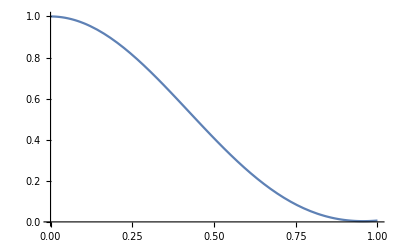

```mathematica
Plot[(Abs[(-0.0044888059292071975-0.0030835466452108773 ⅈ) ((0.+0. ⅈ)-(0.004488805929207248-0.003083546645210958 ⅈ) (ⅇ^(-5.561936878925514*^-17 t) Cos[0.5000290537481847 t]-ⅈ ⅇ^(-5.561936878925514*^-17 t) Sin[0.5000290537481847 t]))-(0.0018790218966102386-0.02770617213497778 ⅈ) ((0.+0. ⅈ)-(0.001879021896610166+0.027706172134977575 ⅈ) (ⅇ^(3.4499370700050383*^-18 t) Cos[1.4992548206391396 t]-ⅈ ⅇ^(3.4499370700050383*^-18 t) Sin[1.4992548206391396 t]))+(0.011579126277914617+0.06355600297148 ⅈ) ((0.+0. ⅈ)+(0.011579126277914895-0.0635560029714799 ⅈ) (ⅇ^(2.776845082228444*^-16 t) Cos[2.506797330492781 t]-ⅈ ⅇ^(2.776845082228444*^-16 t) Sin[2.506797330492781 t]))-(0.05642511493913981+0.18868864570029634 ⅈ) ((0.+0. ⅈ)-(0.0564251149391398-0.18868864570029606 ⅈ) (ⅇ^(-8.586884256042083*^-16 t) Cos[3.4478414432392657 t]-ⅈ ⅇ^(-8.586884256042083*^-16 t) Sin[3.4478414432392657 t]))-(0.1326833883178345-0.2428692655743969 ⅈ) ((0.+0. ⅈ)-(0.1326833883178347+0.24286926557439706 ⅈ) (ⅇ^(2.3175758073389285*^-15 t) Cos[4.69520688647105 t]-ⅈ ⅇ^(2.3175758073389285*^-15 t) Sin[4.69520688647105 t]))-(0.15720006135608458-0.43592379563590516 ⅈ) ((0.+0. ⅈ)-(0.15720006135608453+0.4359237956359049 ⅈ) (ⅇ^(2.664568134566641*^-15 t) Cos[5.007974750645004 t]-ⅈ ⅇ^(2.664568134566641*^-15 t) Sin[5.007974750645004 t]))+(0.07301069240373995+0.4902750886930593 ⅈ) ((0.+0. ⅈ)+(0.07301069240373996-0.49027508869305925 ⅈ) (ⅇ^(8.878914872892428*^-16 t) Cos[6.538290416822995 t]-ⅈ ⅇ^(8.878914872892428*^-16 t) Sin[6.538290416822995 t]))-(0.3682356133705909+0.5325495958422863 ⅈ) ((0.+0. ⅈ)-(0.36823561337059085-0.5325495958422863 ⅈ) (1. Cos[8.791328160634391 t]-(0.+1. ⅈ) Sin[8.791328160634391 t]))])^2,{t,0,1},PlotRange->{0,1}]
```